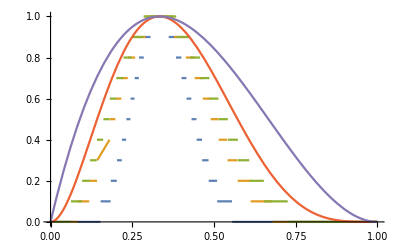

```mathematica
Plot[{Round[205891132094649/1048576(x(1-x)^2)^10,0.1],Round[531441/256 x^4 (1-x)^8,0.1],Round[19683/64 x^3 (1-x)^6,0.1],729/16 x^2 (1-x)^4,6.75*x^1*(1-x)^2},{x,0,1}]
```

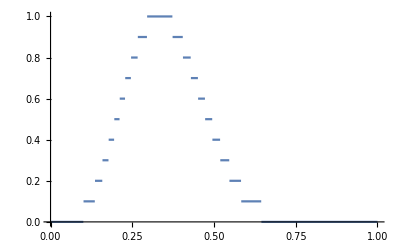

```mathematica
Plot[Round[(6.75 x(1-x)^2)^5,0.1],{x,0,1}]
```

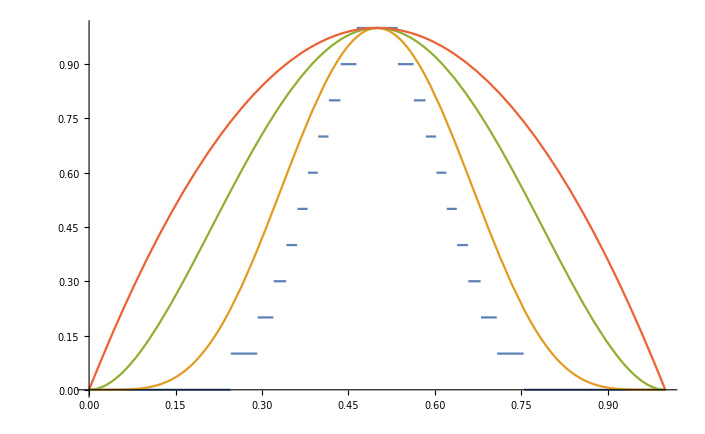

```mathematica
Plot[{Round[(4x(1-x))^10,0.1],(4x(1-x))^5,(4x(1-x))^2,(4x(1-x))^1},{x,0,1}]
```

```mathematica
N[205891132094649/1048576]==196353084.65447330474853515625
```

True

```mathematica
(205891132094649/1048576)^(1/10)
```

27/4

```mathematica
N[27/4]
```

6.75

1.9635308465447330474853515625×10^8

```mathematica
531441/256 x^4 (1-x)^8/.x->0.0835
```

0.0502367

```mathematica
19683/64 x^3 (1-x)^6/.x->0.082
```

0.101487

```mathematica
Solve[D[x^m*(1-x)^n,x]==0,x]
```

{{x→m/(m+n)}}

```mathematica
F[m_,n_]:=Simplify[x^-m*(1-x)^-n/.x->m/(m+n)]
```

```mathematica
F[4,8]
```

531441/256

```mathematica
F[10,20]
```

205891132094649/1048576

```mathematica
F[m,n]
```

(m/(m+n))^-m (n/(m+n))^-n

```mathematica
F[3,9]
```

16777216/19683

```mathematica
Together[729/16*x^2*(1-x)^4]
```

729/16 (-1+x)^4 x^2

```mathematica
N[729/16]
```

```mathematica
45.5625==729/16
```

True

```mathematica
45.5625
```

45.5625

```mathematica
N[19683/64]
```

307.547

```mathematica
307.546875
```

```mathematica
N[531441/256]
```

2075.94